```mathematica
ClearAll[P12,P15,P23,P24,P27,P37,P38,P46,P54,P56,P68,P71,P77,P81,P88,q12,q15,q23,q24,q27,q37,q38,q46,q54,q56,q68,q71,q77,q81,q88,p,sum,k,accp]
```

```mathematica
cp12=0;cp15=0;cp23=0;cp24=0;cp27=0;cp37=0;cp38=0;cp46=0;cp54=0;cp56=0;cp68=0;cp71=0;cp77=0;cp81=0;cp88=0;min=0;
```

```mathematica
nmax=50000;beta=100;k=1;
q12=RandomReal[];
q15=1-q12;
q23=RandomReal[];
q24=RandomReal[{0,1-q23}];
q27=1-q23-q24;
q37=RandomReal[];
q38=1-q37;
q46=1;
q54=RandomReal[];
q56=1-q54;
q68=1;
q71=RandomReal[];
q77=1-q71;
q81=RandomReal[];
q88=1-q81;
Q=({{0, q12, 0, 0, q15, 0, 0, 0}, {0, 0, q23, q24, 0, 0, q27, 0}, {0, 0, 0, 0, 0, 0, q37, q38}, {0, 0, 0, 0, 0, q46, 0, 0}, {0, 0, 0, q54, 0, q56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q68}, {q71, 0, 0, 0, 0, 0, q77, 0}, {q81, 0, 0, 0, 0, 0, 0, q88}});
Piexp=Re[Eigenvectors[Transpose[Q],1]];
phi[0]=0
```

0

```mathematica
For[i=1,i<nmax,i=i+1,{P12=RandomReal[];
P15=1-P12;
P23=RandomReal[];
P24=RandomReal[{0,1-P23}];
P27=1-P23-P24;
P37=RandomReal[];
P38=1-P37;
P46=1;
P54=RandomReal[];
P56=1-P54;
P68=1;
P71=RandomReal[];
P77=1-P71;
P81=RandomReal[];
P88=1-P81;p=({{0, P12, 0, 0, P15, 0, 0, 0}, {0, 0, P23, P24, 0, 0, P27, 0}, {0, 0, 0, 0, 0, 0, P37, P38}, {0, 0, 0, 0, 0, P46, 0, 0}, {0, 0, 0, P54, 0, P56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, P68}, {P71, 0, 0, 0, 0, 0, P77, 0}, {P81, 0, 0, 0, 0, 0, 0, P88}});
bb=Re[Eigenvectors[Transpose[p],1]];If[Re[Part[bb,1,8]]<0,bb=bb*(-1)];phi[i]=Norm[Piexp-bb];Dphi=phi[i]-phi[i-1];
r=Exp[-beta*Dphi];z=RandomReal[];
If[r>z,{accp[k]=p,k=k+1},indeterminate]}]
```

```mathematica
k
```

26432

```mathematica
sum=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
For[j=25000,j<k,j=j+1,sum=sum+accp[j]];
```

```mathematica
PFinal=sum/(k-25000)
```

{{0,0.410237,0,0,0.589763,0,0,0},{0,0,0.494064,0.26613,0,0,0.239806,0},{0,0,0,0,0,0,0.490385,0.509615},{0,0,0,0,0,1,0,0},{0,0,0,0.503393,0,0.496607,0,0},{0,0,0,0,0,0,0,1},{0.507001,0,0,0,0,0,0.492999,0},{0.403739,0,0,0,0,0,0,0.596261}}

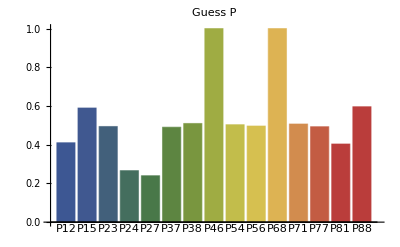

```mathematica
BarChart[{Part[PFinal,1,2],Part[PFinal,1,5],Part[PFinal,2,3],Part[PFinal,2,4],Part[PFinal,2,7],Part[PFinal,3,7],Part[PFinal,3,8],Part[PFinal,4,6],Part[PFinal,5,4],Part[PFinal,5,6],Part[PFinal,6,8],Part[PFinal,7,1],Part[PFinal,7,7],Part[PFinal,8,1],Part[PFinal,8,8]},ChartLabels->{"P12","P15","P23","P24","P27","P37","P38","P46","P54","P56","P68","P71","P77","P81","P88"},ChartStyle->"DarkRainbow",PlotLabel->"Guess P"]
```

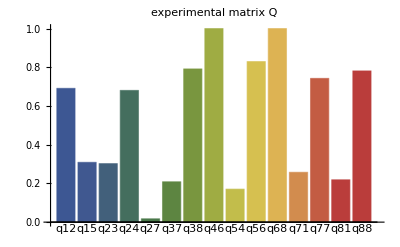

```mathematica
BarChart[{q12,q15,q23,q24,q27,q37,q38,q46,q54,q56,q68,q71,q77,q81,q88},ChartLabels->{"q12","q15","q23","q24","q27","q37","q38","q46","q54","q56","q68","q71","q77","q81","q88"},ChartStyle->"DarkRainbow",PlotLabel->"experimental matrix Q"]
```

```mathematica
For[q=1,q<k-1,q=q+1,
{min=Min[Part[accp[q],1,2],Part[accp[q],1,5],Part[accp[q],2,3],Part[accp[q],2,4],Part[accp[q],2,7],Part[accp[q],3,7],Part[accp[q],3,8],Part[accp[q],4,6],Part[accp[q],5,4],Part[accp[q],5,6],Part[accp[q],6,8],Part[accp[q],7,1],Part[accp[q],7,7],Part[accp[q],8,1],Part[accp[q],8,8]];
If[Part[accp[q],1,2]==min,cp12=cp12+1];
If[Part[accp[q],1,5]==min,cp15=cp15+1];
If[Part[accp[q],2,3]==min,cp23=cp23+1];
If[Part[accp[q],2,4]==min,cp24=cp24+1];
If[Part[accp[q],2,7]==min,cp27=cp27+1];
If[Part[accp[q],3,7]==min,cp37=cp37+1];
If[Part[accp[q],3,8]==min,cp38=cp38+1];
If[Part[accp[q],4,6]==min,cp46=cp46+1];
If[Part[accp[q],5,4]==min,cp54=cp54+1];
If[Part[accp[q],5,6]==min,cp56=cp56+1];
If[Part[accp[q],6,8]==min,cp68=cp68+1];
If[Part[accp[q],7,1]==min,cp71=cp71+1];
If[Part[accp[q],7,7]==min,cp77=cp77+1];
If[Part[accp[q],8,1]==min,cp81=cp81+1];
If[Part[accp[q],8,8]==min,cp88=cp88+1];

}]
```

```mathematica
cpall=Max[cp12,cp15,cp23,cp24,cp27,cp37,cp38,cp46,cp54,cp56,cp68,cp71,cp77,cp81,cp88];
mc12=1-cp12/cpall;
mc15=1-cp15/cpall;
mc23=1-cp23/cpall;
mc24=1-cp24/cpall;
mc27=1-cp27/cpall;
mc37=1-cp37/cpall;
mc38=1-cp38/cpall;
mc46=1-cp46/cpall;
mc54=1-cp54/cpall;
mc56=1-cp56/cpall;
mc68=1-cp68/cpall;
mc71=1-cp71/cpall;
mc77=1-cp77/cpall;
mc81=1-cp81/cpall;
mc88=1-cp88/cpall;
```

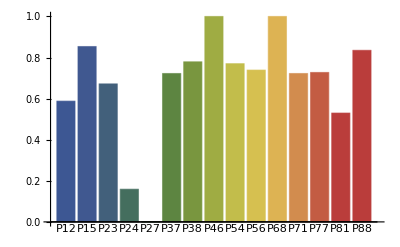

```mathematica
BarChart[{mc12,mc15,mc23,mc24,mc27,mc37,mc38,mc46,mc54,mc56,mc68,mc71,mc77,mc81,mc88},ChartLabels->{"P12","P15","P23","P24","P27","P37","P38","P46","P54","P56","P68","P71","P77","P81","P88"},ChartStyle->"DarkRainbow"]
```